```mathematica
Table[
With[{g=CompleteGraph[k],h=CompleteGraph[k-3]},
With[{res=EdgeDelete[g,EdgeList[h]]},
Labeled[Graph[g,GraphHighlight->Join[EdgeList[h],VertexList[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name"],{FindClique[res],ChromaticPolynomial[res,4]}]
]
],
{k,5,10}]
```

{-Graphics-{{{1,3,4,5}},24},-Graphics-{{{1,4,5,6}},24},-Graphics-{{{1,5,6,7}},24},-Graphics-{{{1,6,7,8}},24},-Graphics-{{{1,7,8,9}},24},-Graphics-{{{1,8,9,10}},24}}

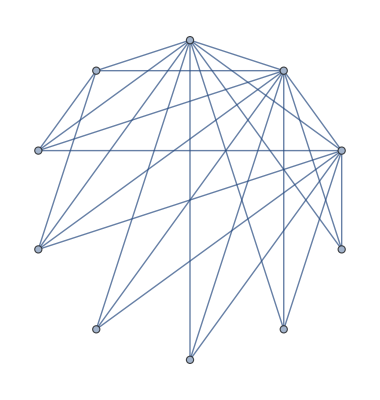

```mathematica
EdgeDelete[CompleteGraph[10],{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->4,1<->8}]
```

```mathematica
Map[First,{{{6<->7,5<->8,4<->9,3<->10,2<->7,2<->6,1<->8,1<->5},1},{{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->9,1<->9,1<->2},10},{{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->9,1<->7,1<->6,1<->5},31},{{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->7,2<->8,2<->9,1<->9,1<->2},79},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->8,2<->8,2<->3,1<->8,1<->3,1<->2},167},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->8,1<->8,1<->2},429},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->8,1<->8,1<->2},781},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->8,1<->8,1<->2},2168},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->8},5698},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->8},9642},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->8},8625},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->8},3524},{{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->4,1<->8},628}}]
```

{{6<->7,5<->8,4<->9,3<->10,2<->7,2<->6,1<->8,1<->5},{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->9,1<->9,1<->2},{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->9,1<->7,1<->6,1<->5},{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->7,2<->8,2<->9,1<->9,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->8,2<->8,2<->3,1<->8,1<->3,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->8,1<->8,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->8,1<->8,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->8,1<->8,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->4,1<->8}}

```mathematica
Table[With[{g=CompleteGraph[10],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
Labeled[Graph[g,GraphHighlight->Join[EdgeList[h],VertexList[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name"],{FindClique[res],ChromaticPolynomial[res,4],Length[edges]}]
]
],
{edges,{{6<->7,5<->8,4<->9,3<->10,2<->7,2<->6,1<->8,1<->5},{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->9,1<->9,1<->2},{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->9,1<->7,1<->6,1<->5},{6<->7,5<->7,5<->6,4<->8,3<->8,3<->4,2<->7,2<->8,2<->9,1<->9,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->8,2<->8,2<->3,1<->8,1<->3,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->8,1<->8,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->8,1<->8,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->8,1<->8,1<->2},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->8},{6<->7,5<->7,5<->6,4<->7,4<->6,4<->5,3<->7,3<->6,3<->5,3<->4,2<->7,2<->6,2<->5,2<->4,2<->3,1<->7,1<->6,1<->5,1<->4,1<->8}}}
]
```

{-Graphics-{{{1,2,3,4}},24,8},-Graphics-{{{1,3,5,10}},24,9},-Graphics-{{{1,2,3,10}},24,10},-Graphics-{{{1,3,5,10}},24,11},-Graphics-{{{1,4,9,10}},24,12},-Graphics-{{{1,3,9,10}},24,13},-Graphics-{{{1,3,9,10}},24,14},-Graphics-{{{1,3,9,10}},24,15},-Graphics-{{{1,2,9,10}},24,16},-Graphics-{{{1,2,9,10}},24,17},-Graphics-{{{1,2,9,10}},24,18},-Graphics-{{{1,2,9,10}},24,19},-Graphics-{{{1,2,9,10}},24,20}}

```mathematica
Table[With[{g=CompleteGraph[11],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
Labeled[Graph[g,GraphHighlight->Join[EdgeList[h],VertexList[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name"],{FindClique[res],ChromaticPolynomial[res,4],Length[edges]}]
]
],
{edges,{{7<->8,6<->8,6<->7,5<->9,4<->9,4<->5,3<->10,2<->10,2<->3,1<->11}}}
]
```

{-Graphics-{{{1,2,4,6}},24,10}}

```mathematica
Map[First,{{{4<->5,3<->6,2<->7,1<->8},1},{{4<->5,3<->6,2<->7,1<->5,1<->6,1<->7,1<->8},1},{{4<->5,3<->6,2<->7,1<->5,1<->6,1<->3},1},{{4<->5,3<->6,2<->7,1<->5,1<->4},1},{{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3},1},{{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->2},2},{{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->6,1<->3},1},{{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->4},1},{{4<->5,3<->5,3<->6,2<->6,2<->4,1<->7},1},{{4<->5,3<->5,3<->6,2<->6,2<->4,1<->5,1<->4,1<->7},1},{{4<->5,3<->5,3<->4,2<->6,1<->6,1<->2},2},{{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->4,1<->2},7},{{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->2},8},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->3},8},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->2},10},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->6},3},{{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->6},11}}]
```

{{4<->5,3<->6,2<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->7,1<->5,1<->4},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->2},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->4},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->7},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->5,1<->4,1<->7},{4<->5,3<->5,3<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->4,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->3},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->6},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->6}}

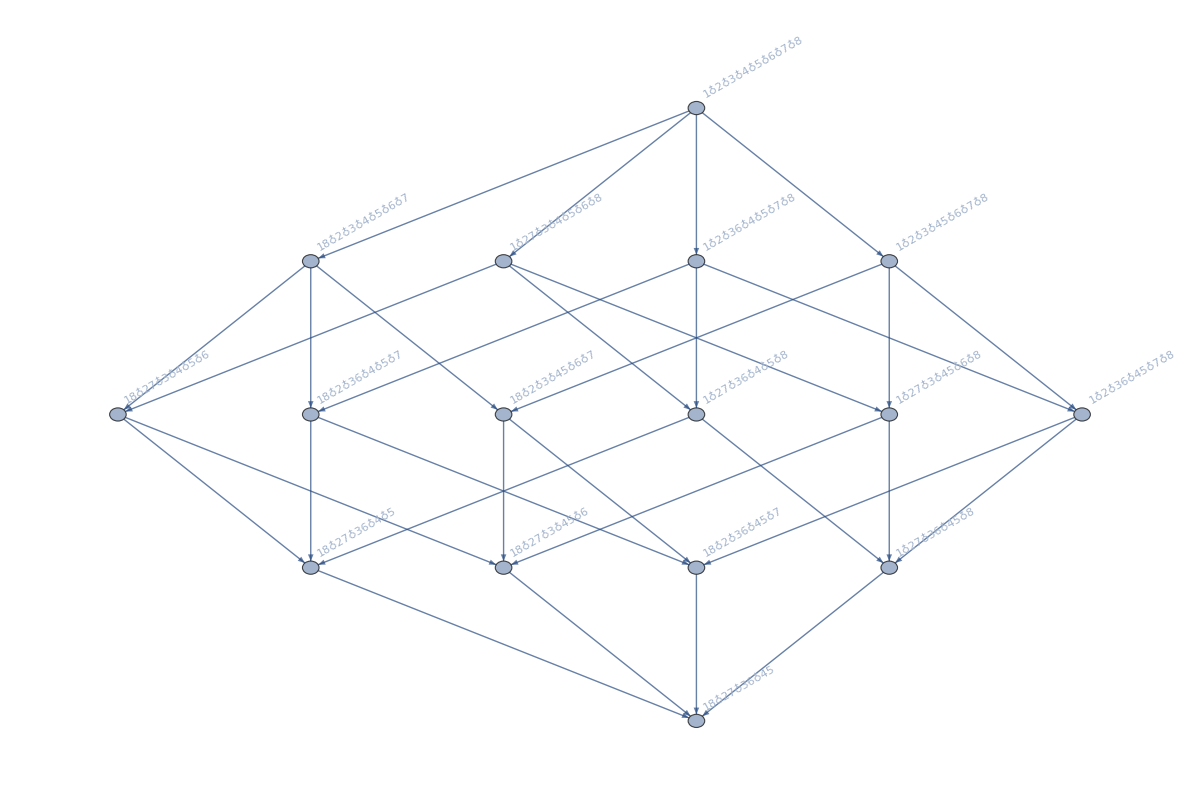
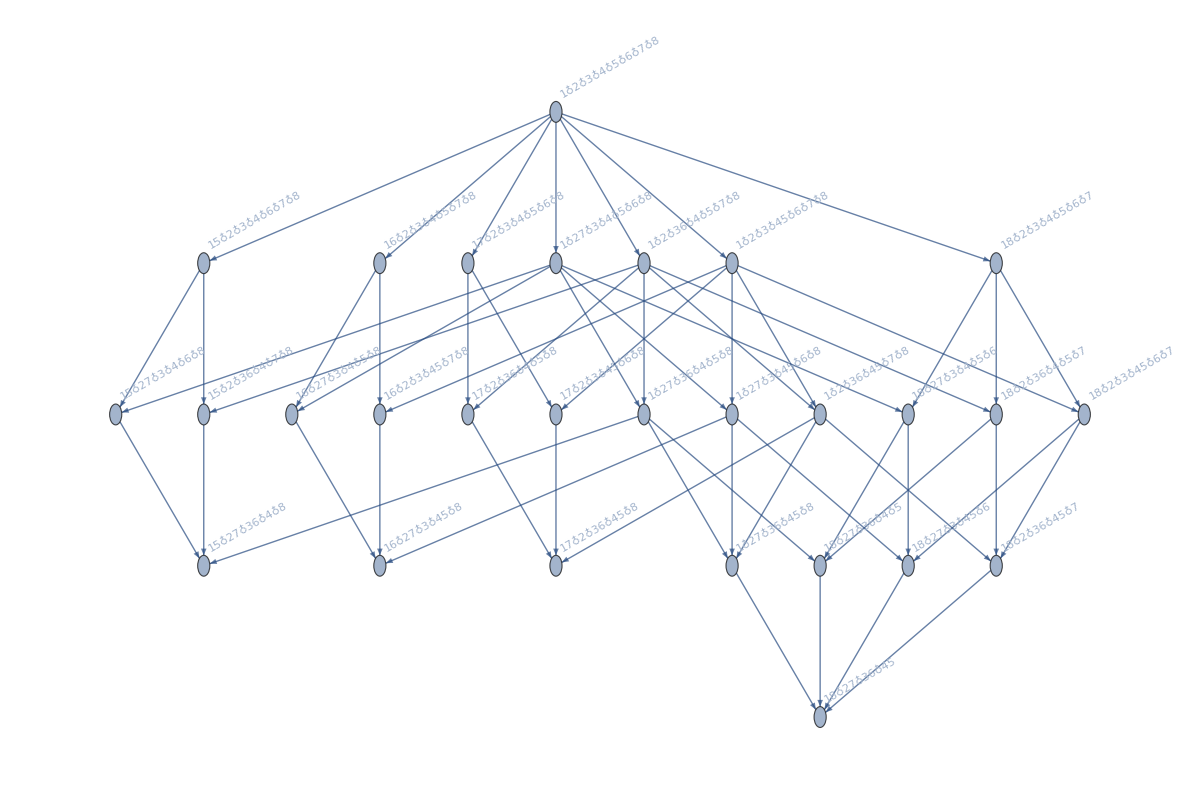
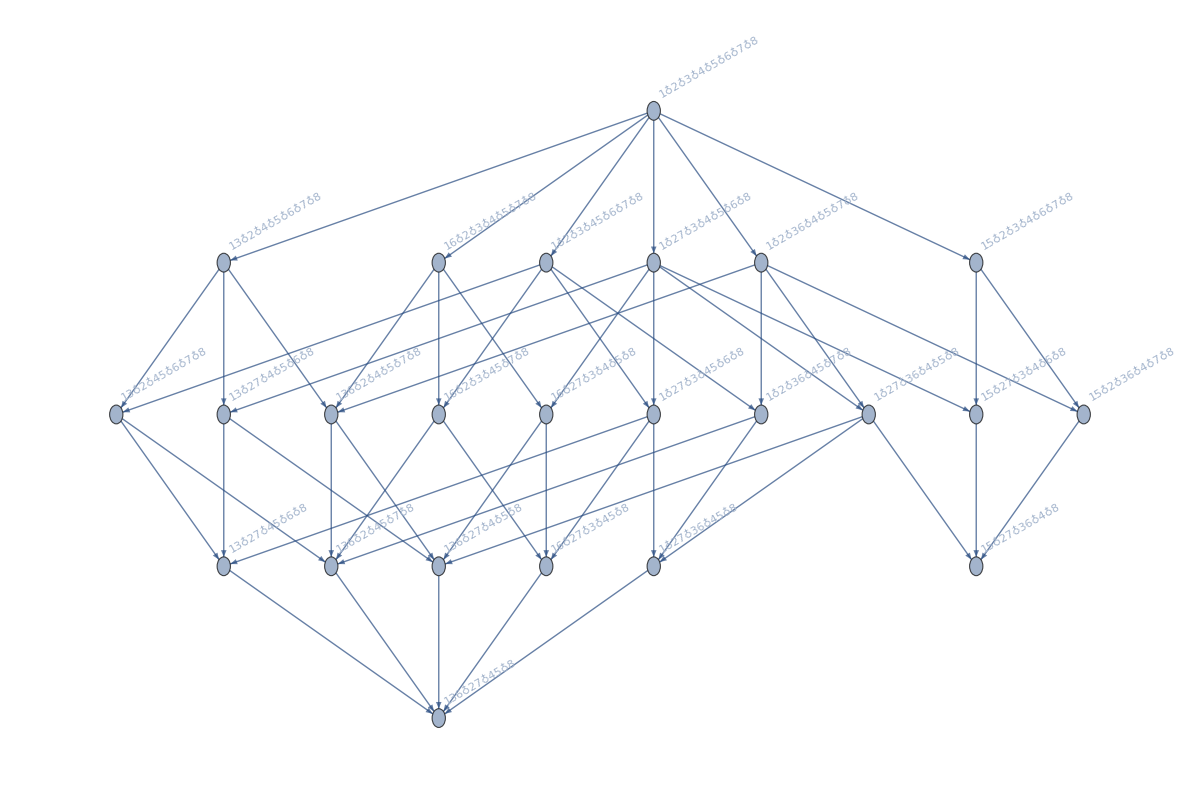
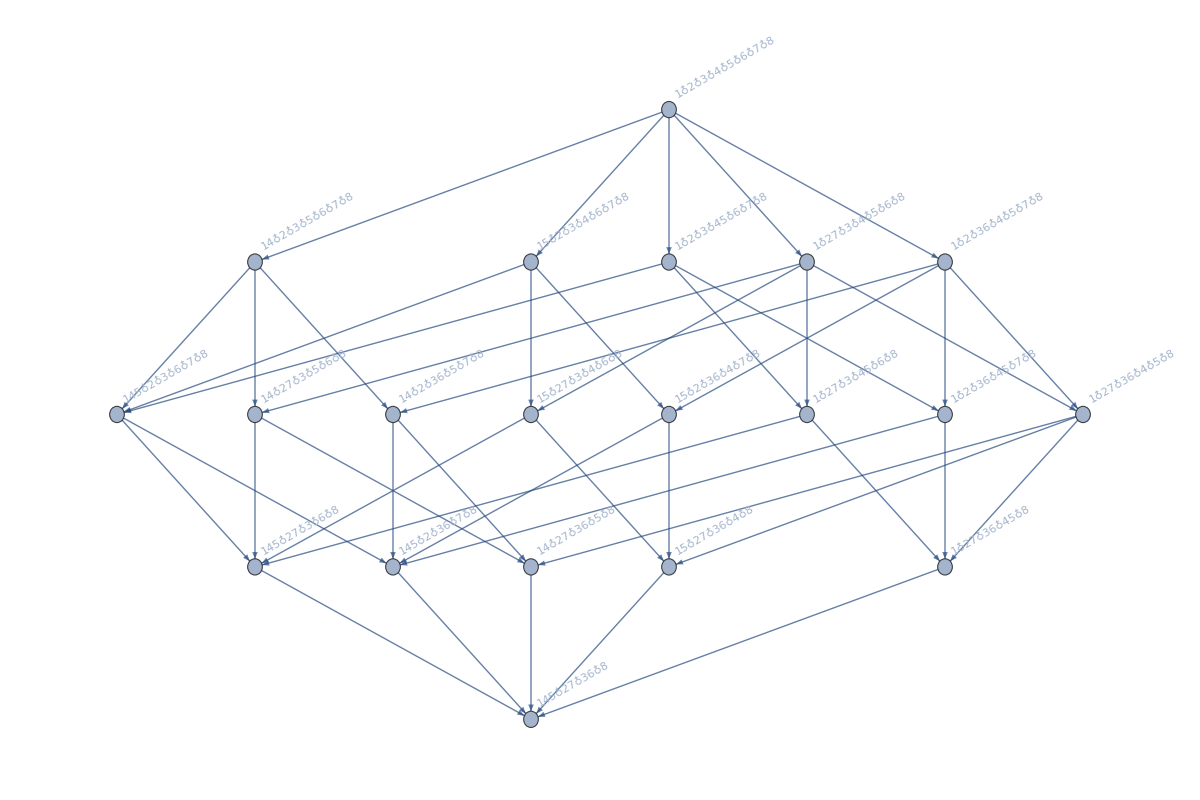
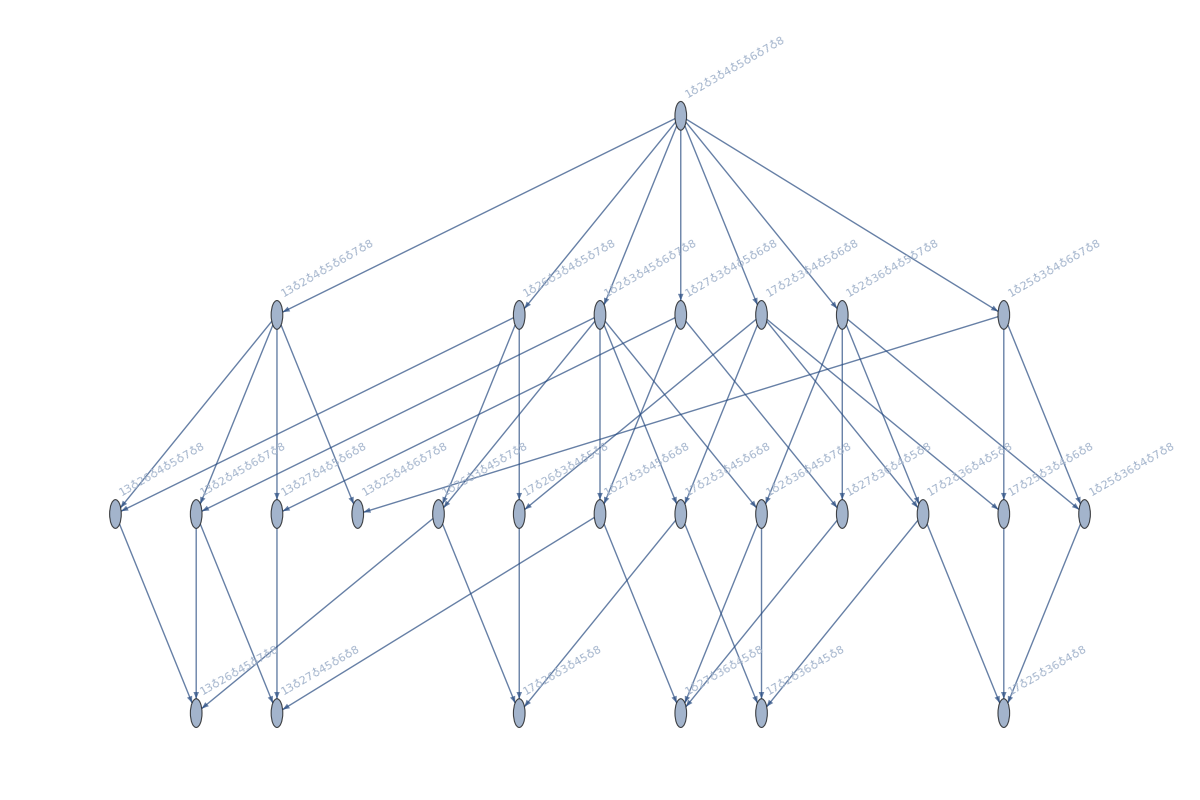
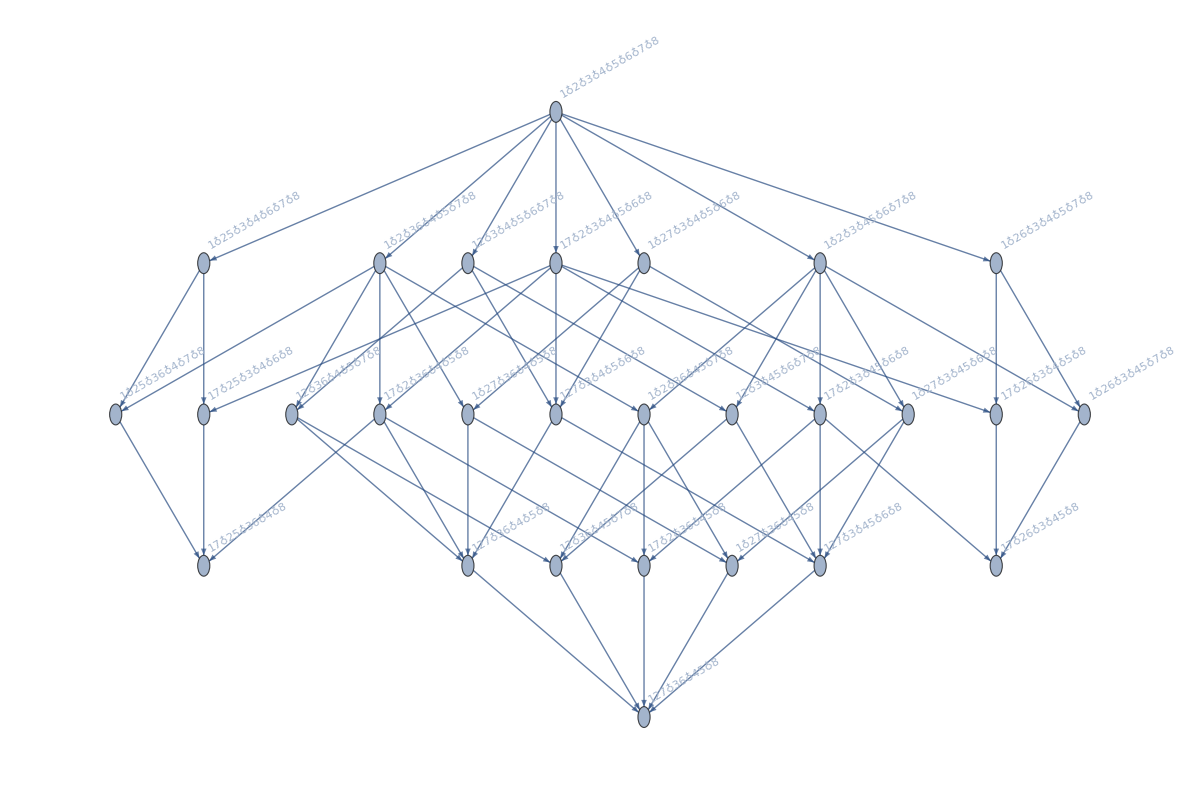
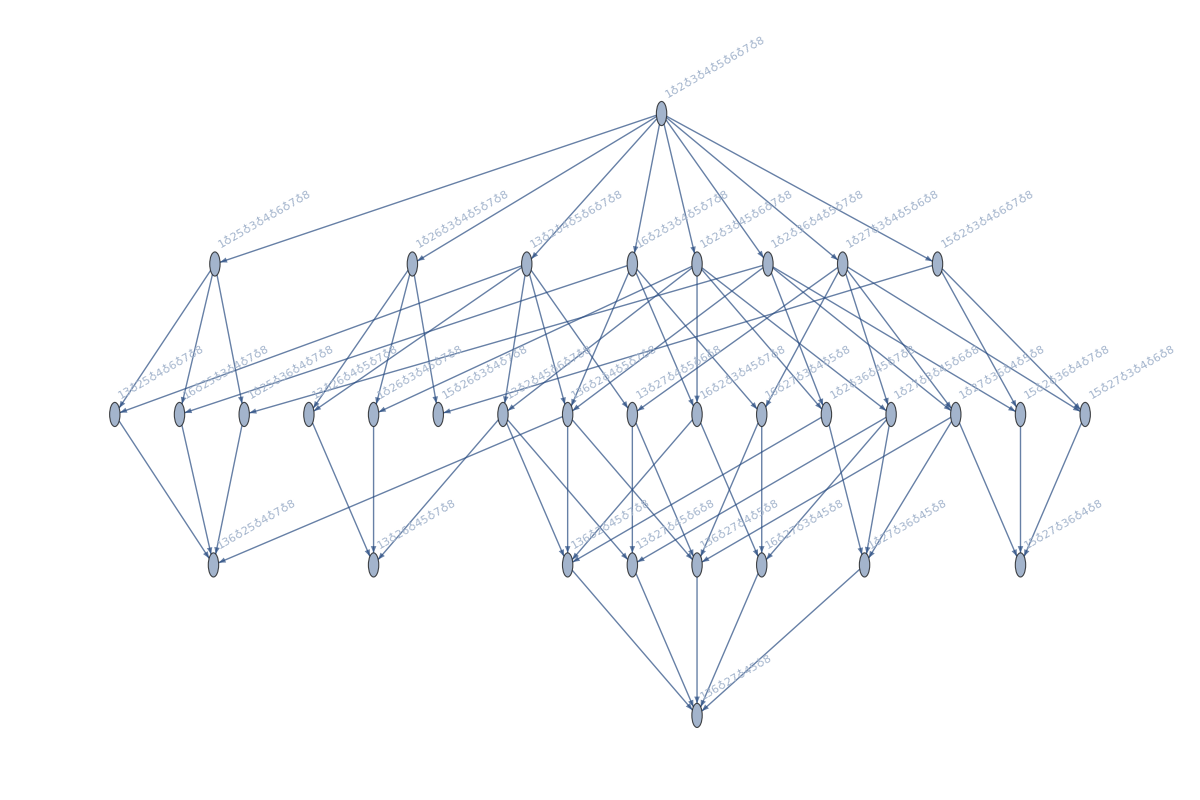
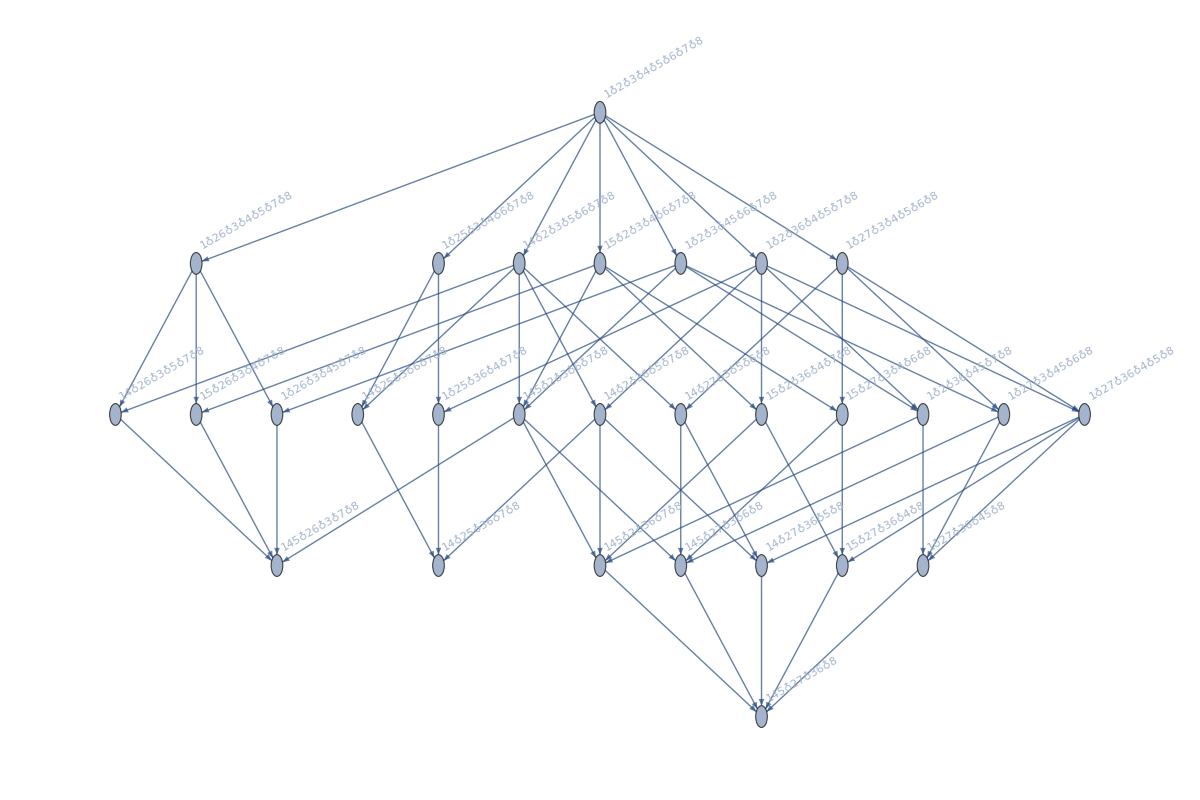
{-Graphics-{{{1,2,3,4}},24,4}→-Graphics-,-Graphics-{{{1,2,3,4}},24,7}→-Graphics-,-Graphics-{{{1,2,4,8}},24,6}→-Graphics-,-Graphics-{{{1,2,3,8}},24,5}→-Graphics-,-Graphics-{{{1,2,4,8}},0,7}→-Graphics-,-Graphics-{{{1,3,4,8}},24,7}→-Graphics-,-Graphics-{{{1,2,4,8}},24,8}→-Graphics-,-Graphics-{{{1,2,3,8}},24,7}→-Graphics-,-Graphics-{{{1,2,3,8}},0,6}→-Graphics-,-Graphics-{{{1,2,3,8}},0,8}→-Graphics-,-Graphics-{{{1,3,7,8}},24,6}→-Graphics-,-Graphics-{{{1,3,7,8}},24,8}→-Graphics-,-Graphics-{{{1,3,7,8}},24,7}→-Graphics-,-Graphics-{{{1,2,7,8}},0,8}→-Graphics-,-Graphics-{{{1,3,7,8}},24,8}→-Graphics-,-Graphics-{{{1,2,7,8}},24,7}→-Graphics-,-Graphics-{{{1,2,7,8}},24,8}→-Graphics-}

```mathematica
Table[With[{g=CompleteGraph[8],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
Labeled[Graph[g,GraphHighlight->Join[EdgeList[h],VertexList[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name"],{FindClique[res],ChromaticPolynomial[res,4],Length[edges]}]->Graph[FormulaGraphReverse2[FindFullFormula[res]],ImageSize->{1200,800}]
]
],
{edges,{{4<->5,3<->6,2<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->7,1<->5,1<->4},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->2},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->4},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->7},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->5,1<->4,1<->7},{4<->5,3<->5,3<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->4,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->3},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->6},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->6}}}
]
```

```mathematica
Table[With[{g=CompleteGraph[12],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
Labeled[Graph[g,GraphHighlight->Join[EdgeList[h],VertexList[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name"],{FindClique[res],ChromaticPolynomial[res,4],Length[edges]}]
]
],
{edges,{{8<->9,7<->9,7<->8,6<->10,5<->10,5<->6,4<->11,3<->11,3<->4,2<->12,1<->12,1<->2}}}
]
```

{-Graphics-{{{1,3,5,7}},24,12}}

```mathematica
{9<->10,8<->10,8<->9,7<->11,6<->11,6<->7,5<->12,4<->12,4<->5,3<->13,2<->13,2<->3,1<->10,1<->9,1<->8}
```

```mathematica
Table[With[{g=CompleteGraph[13],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
Labeled[Graph[g,GraphHighlight->Join[EdgeList[h],VertexList[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name"],{FindClique[res],ChromaticPolynomial[res,4],Length[edges]}]
]
],
{edges,{{9<->10,8<->10,8<->9,7<->11,6<->11,6<->7,5<->12,4<->12,4<->5,3<->13,2<->13,2<->3,1<->10,1<->9,1<->8}}}
]
```

{-Graphics-{{{1,2,4,6}},24,15}}

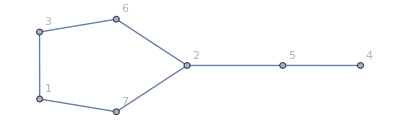
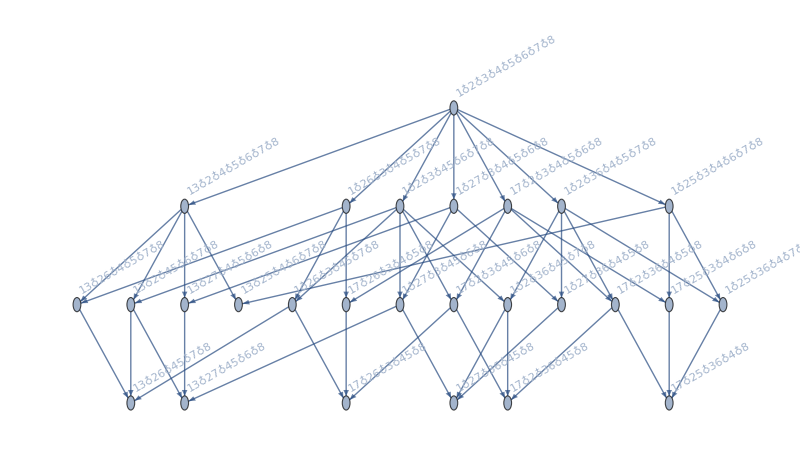
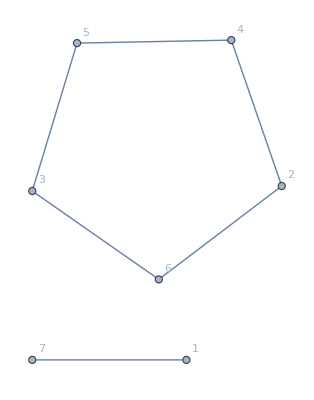
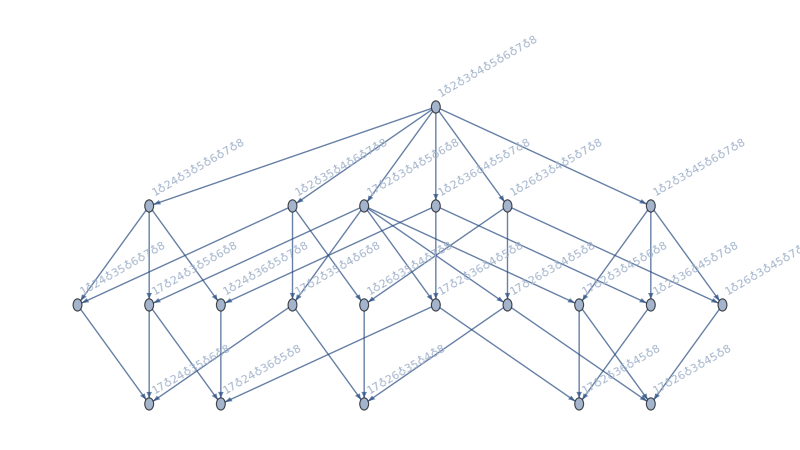
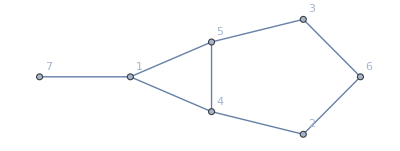
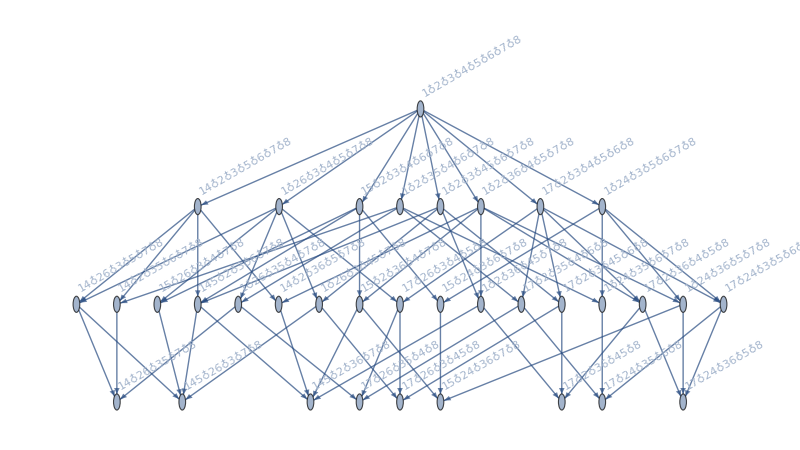
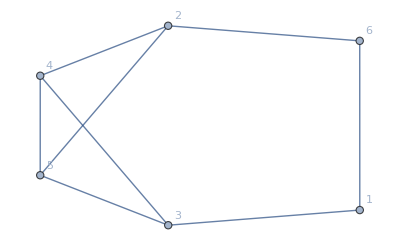
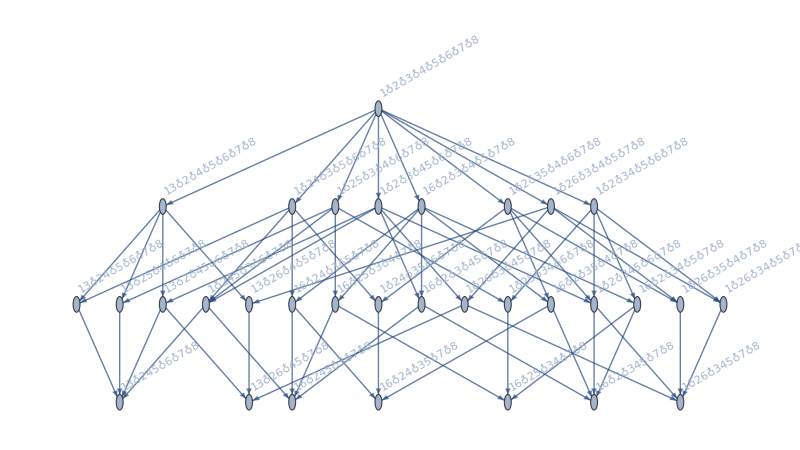
{-Graphics-,-Graphics-{{{1,2,4,8}},0,7},-Graphics-,-Graphics-,-Graphics-{{{1,2,3,8}},0,6},-Graphics-,-Graphics-,-Graphics-{{{1,2,3,8}},0,8},-Graphics-,-Graphics-,-Graphics-{{{1,2,7,8}},0,8},-Graphics-}

```mathematica
Select[Table[With[{g=CompleteGraph[8],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
If[ChromaticPolynomial[res,4]==0,
{Graph[h,  VertexLabels->"Name"],Labeled[Graph[g,GraphHighlight->Join[EdgeList[h],VertexList[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name"],{FindClique[res],ChromaticPolynomial[res,4],Length[edges]}],Graph[FormulaGraphReverse2[FindFullFormula[res]]
,ImageSize->{800,450}]}]
]
],
{edges,{{4<->5,3<->6,2<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->7,1<->5,1<->4},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->2},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->4},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->7},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->5,1<->4,1<->7},{4<->5,3<->5,3<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->4,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->3},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->6},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->6}}}
],#=!=Null&]//Flatten
```

```mathematica
Table[With[{g=CompleteGraph[15],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
Labeled[Graph[g,GraphHighlight->Join[EdgeList[h],VertexList[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name"],{FindClique[res],ChromaticPolynomial[res,4],Length[edges]}]
]
],
{edges,{EdgeList[CycleGraph[15]]}}
]
```

{-Graphics-{{{1,3,5,7,9,11,13}},0,15}}

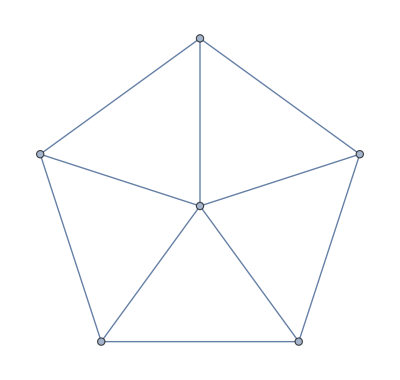

```mathematica
WheelGraph[6]
```

```mathematica
Table[With[{g=CompleteGraph[11],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
Labeled[Graph[g,GraphHighlight->Join[EdgeList[h],VertexList[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name"],{FindClique[res],ChromaticPolynomial[res,4],Length[edges],VertexCount[g]*3-6,Binomial[VertexCount[g],2]}]
]
],
{edges,{EdgeList[CompleteGraph[11-3]]}}
]
```

{-Graphics-{{{1,9,10,11}},24,28,27,55}}

```mathematica
IntegerPartitions[11,{4}]
```

{{8,1,1,1},{7,2,1,1},{6,3,1,1},{6,2,2,1},{5,4,1,1},{5,3,2,1},{5,2,2,2},{4,4,2,1},{4,3,3,1},{4,3,2,2},{3,3,3,2}}